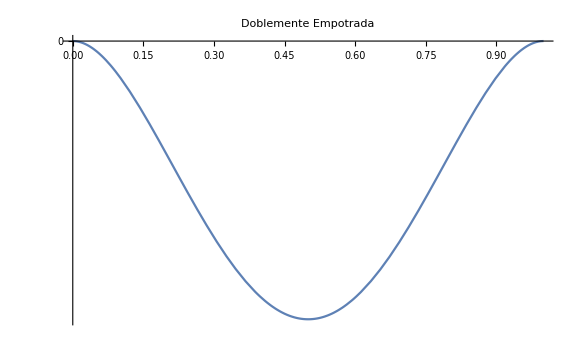

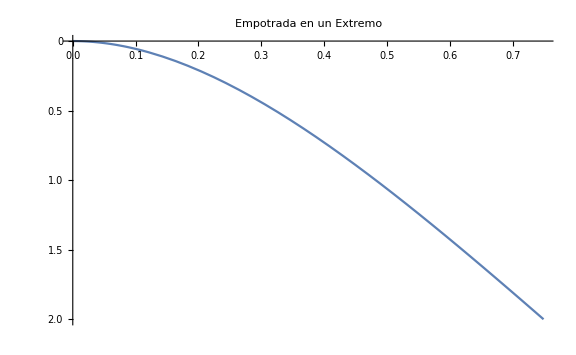

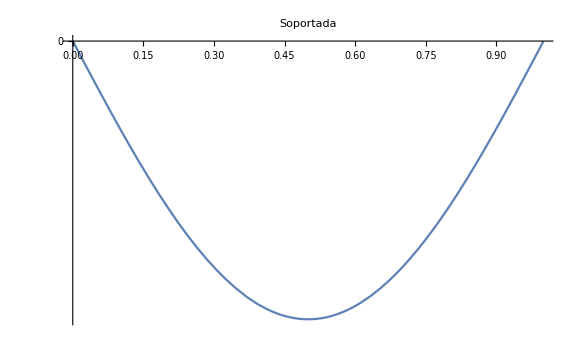

```mathematica
EI=1;
w=24;
L=1;
paso=0.1;

sol1 = NDSolve[{EI*y''''[x]==w,y[0]==0,y'[0]==0,y[L]==0,y'[L]==0},y,{x,0,1},StartingStepSize->paso,Method->"ExplicitRungeKutta"];
sol2 = NDSolve[{EI*y''''[x]==w,y[0]==0,y'[0]==0,y''[L]==0,y'''[L]==0},y,{x,0,1},StartingStepSize->paso,Method->"ExplicitRungeKutta"];
sol3 = NDSolve[{EI*y''''[x]==w,y[0]==0,y''[0]==0,y[L]==0,y''[L]==0},y,{x,0,1},StartingStepSize->paso,Method->"ExplicitRungeKutta"];

f[x_]=y[x]/.sol1[[1]];
g[x_]=y[x]/.sol2[[1]];
h[x_]=y[x]/.sol3[[1]];

Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ImageSize->Large, ScalingFunctions->"Reverse",PlotLabel->HoldForm[Doblemente Empotrada]]
Plot[g[x],{x,0,1},PlotRange->{{0,2},{0,2}},ImageSize->Large, ScalingFunctions->"Reverse",PlotLabel->HoldForm[Empotrada en un Extremo]]
Plot[h[x],{x,0,1},PlotRange->{{0,1},{0,4}},ImageSize->Large, ScalingFunctions->"Reverse",PlotLabel->HoldForm[Soportada]]
```